# Complex Newton’s Method

Adam Rumpf, 2/23/2016

## Introduction

Newton’s method (a.k.a. the Newton-Raphson method) is an iterative root finding process. Given a function f and an initial guess x_0, the process is defined by:

x_(n+1)=x_n-(f(x_n))/(f'(x_n))

This method is taught in basic Calculus, and it is mostly of interest because it is (a) simple to define and understand, (b) easy to visualize, and (c) good enough to still be used for scientific computing, despite being over 300 years old.

Many students will be surprised to know that this method does not just work for real-valued functions: it works for complex-valued functions, as well. Its behavior in the complex plane can be a bit more complicated to describe, and depending on the initial guess, the method may not necessarily converget to the nearest root.

This Notebook defines a function called newtonplot[], which accepts (in order) a pure function, a bound b for the complex domain [-b,b]×[-b,b], the number of nodes n into which each axis will be divided, an iteration cutoff, and an error tolerance. The function will divide the square domain into an n×n grid and conduct Newton’s method using every grid node as an initial guess. If the method comes within the error tolerance of one of the true roots, then the method terminates and we record which root was reached. If no root is reached within the iteration cutoff, then the process is deemed to have diverged.

The output is a coloring of the complex domain showing which initial guesses converge to which roots. A larger value of n will lead to a sharper picture but a longer computation time.

## Code

### Initialization

```mathematica
(* roots[f] returns a list of the unique roots of function f. *)
roots[f_]:=Module[{r},
r=DeleteDuplicates[x/.Solve[f[x]==0,x]];
Table[Re[r[[i]]]+I Im[r[[i]]],{i,1,Length[r]}]
];
```

```mathematica
roots[Function[x,x^3-1]]
```

{1,-1/2-(ⅈ √3)/2,-1/2+(ⅈ √3)/2}

```mathematica
(* newtonplot[f,lim,n,cut,eps] creates a plot of the region [-lim,lim]x[-lim,lim] of the complex plane, divided into an nxn grid.  Each grid point is used as the initial guess for complex Newton's method on function f.  Each root is assigned a color, and after cut iterations, if we are within distance eps of a root, we assign that point that root's color.  If if is not that close to any root, we color it black. *)
newtonplot[f_,lim_,n_,cut_,eps_]:=Module[{fp,newton,rootlist,array,grid,dx,i,j,iter,x,numroots,rootnum},
(* fp = derivative of f
newton = Newton's method iteration function
rootlist = list of all unique roots of f
array = array of values corresponding to each grid point (-1 means no root, positive integer corresponds to one of the roots in the list)
grid = array of actual coordinates of grid points
dx = space between grid points
i,j = coordinates of point currently being examined
iter = current iteration of Newton's Method
x = current guess in Newton's Method
numroots = number of roots
rootnum = index of root under evaluation *)
fp=Function[x,f'[x]];
newton=Function[x,N[x-f[x]/fp[x]]];
rootlist=roots[f];
numroots=Length[rootlist];
dx=(2lim)/(n-1);
array=ConstantArray[-1,{n,n}];
grid=Table[N[(-lim+l dx)+I(-lim+k dx)],{k,n-1,0,-1},{l,0,n-1}];
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
x=grid[[i,j]];
For[iter=1,iter≤cut,iter++,
If[fp[x]≠0&&Abs[x]≠Infinity,
x=newton[x],
x=ComplexInfinity;
];
];
For[rootnum=1,rootnum≤numroots,rootnum++,
If[Abs[x-rootlist[[rootnum]]]<eps,
array[[i,j]]=rootnum;
];
];
];
];
ArrayPlot[array,ColorRules->Join[{-1->Black},Table[k->Hue[(k-1)/numroots],{k,1,numroots}]],PlotLegends->Join[{"Divergent"},Table[rootlist[[k]],{k,1,numroots}]]]
];
```

### Demonstration

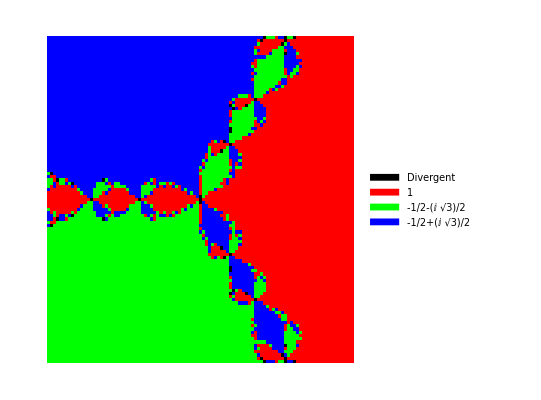

```mathematica
newtonplot[Function[x,x^3-1],2,101,20,0.05]
```

```mathematica
newtonplot[Function[x,x^3-1],2,501,20,0.05]
```

-Graphics-

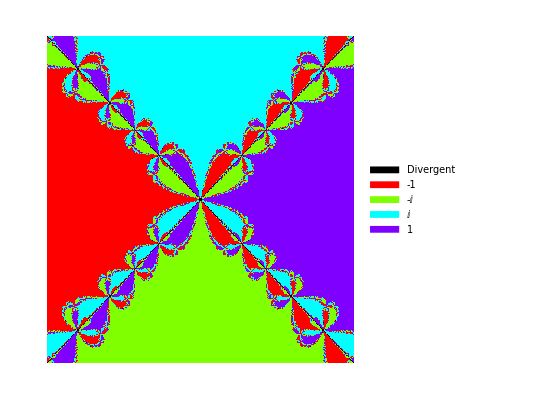

```mathematica
newtonplot[Function[x,x^4-1],2,401,40,0.1]
```

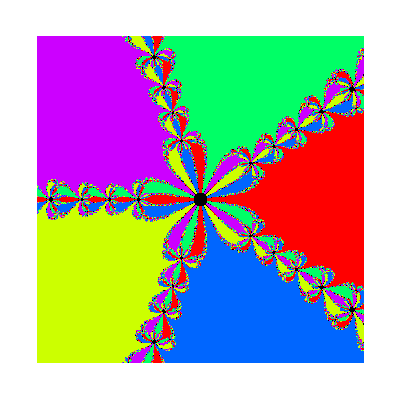

```mathematica
newtonplot[Function[x,x^5-1],2,401,40,0.1]
```

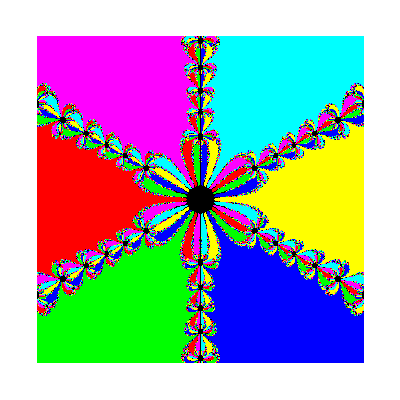

```mathematica
newtonplot[Function[x,x^6-1],2,401,40,0.1]
```

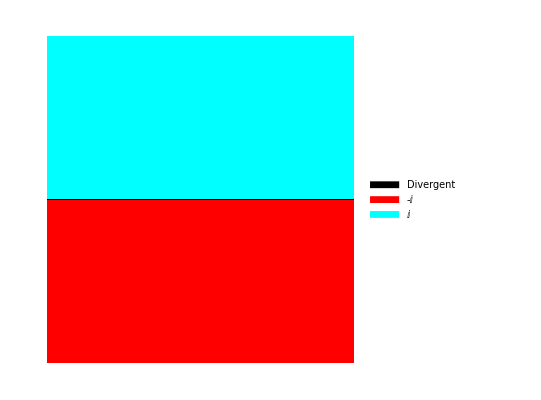

```mathematica
newtonplot[Function[x,x^2+1],2,201,20,0.05]
```

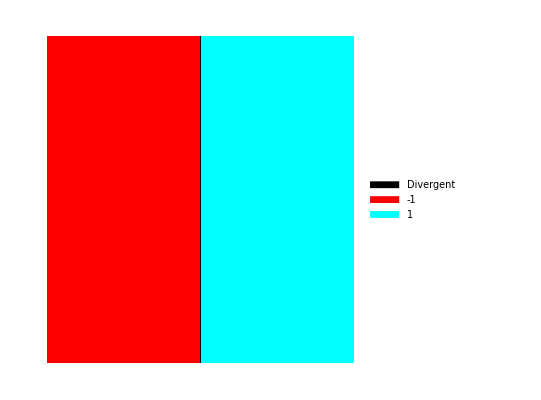

```mathematica
newtonplot[Function[x,x^2-1],2,201,20,0.05]
```

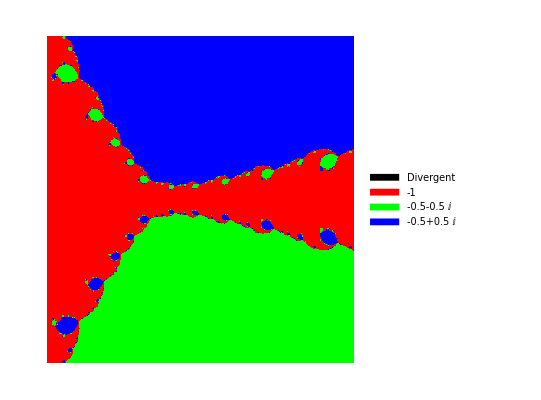

```mathematica
newtonplot[Function[x,(x+1)(x-(-0.5+0.5I))(x-(-0.5-0.5I))],2,401,20,0.05]
```

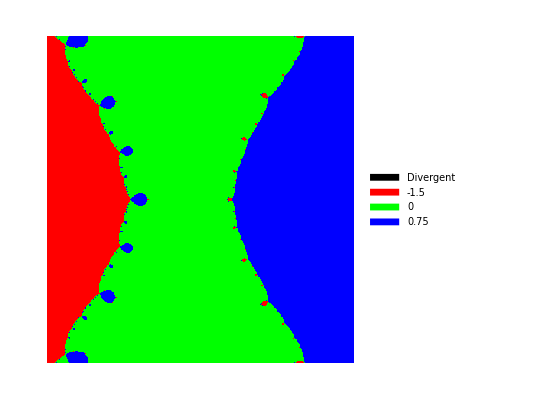

```mathematica
newtonplot[Function[x,(x+1.5)(x)(x-0.75)],2,401,20,0.05]
```